```mathematica
Remove["Global`*"];

PDF1 = ((4*s)/ (π*R*R))*ArcCos[s/(2*R)]-((2*s*s)/(π*R*R*R))*Sqrt[1-((s*s)/(4*R*R))]
```

-(2 s^2 √(1-s^2/(4 R^2)))/(π R^3)+(4 s ArcCos[s/(2 R)])/(π R^2)

```mathematica
a={s∈Reals,R∈Reals,s >0, R>= 0 , s ≤ 2*R };
```

```mathematica
CDF1 = Simplify[Integrate[PDF1, s, Assumptions->a],a]
```

(-1/4 √(4-s^2/R^2) (2 R^2 s+s^3)+2 R s^2 ArcCos[s/(2 R)]+2 R^3 ArcSin[s/(2 R)])/(π R^3)

```mathematica
TeXForm[PDF1]
```

\frac{4 s \cos ^{-1}\left(\frac{s}{2 R}\right)}{\pi  R^2}-\frac{2 s^2 \sqrt{1-\frac{s^2}{4 R^2}}}{\pi  R^3}

```mathematica
TeXForm[CDF1]
```

\frac{2 R^3 \sin ^{-1}\left(\frac{s}{2 R}\right)-\frac{1}{4} \sqrt{4-\frac{s^2}{R^2}} \left(2 R^2 s+s^3\right)+2 R s^2 \cos
   ^{-1}\left(\frac{s}{2 R}\right)}{\pi  R^3}

```mathematica
CForm[CDF1]
```

(-(Sqrt(4 - Power(s,2)/Power(R,2))*(2*Power(R,2)*s + Power(s,3)))/4. + 2*R*Power(s,2)*ArcCos(s/(2.*R)) + 
     2*Power(R,3)*ArcSin(s/(2.*R)))/(Pi*Power(R,3))

```mathematica
R=4
```

4

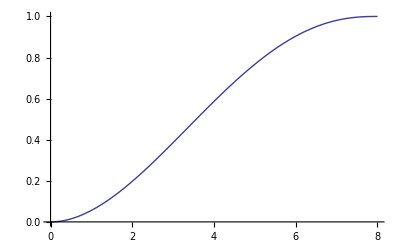

```mathematica
Plot[{CDF1},{s,0,2*R}]
```